## Необходимо определить, как меняется напряженность электромагнитного поля в заданной области.

```mathematica
ψ=10^5;
β = 10^6;
ϕ=10^8;
T=10^-7;
w = 10^9;
p[t_]:=(1-2/(ⅇ^(-ϕ t)+ⅇ^(ϕ t)));    (* граничные функции *)
ex[t_]:=p[t]*(1 - 1/(1+β*(Sin[ψ*t])^2))*(Sin[ψ*t])^2*Sin[w*t];
ey[t_]:=p[t]*(1 - 1/(1+β*(Sin[ψ*t])^2))*(Sin[ψ*t])^2*Cos[w*t];

(* начальные данные *)
ξ0=8.85 10^-12;
μ0=4π 10^-6;
ξ1=1.0005;
μ1=0.9999;
ξ2=8;
μ2=0.9999;
λ1=0.00001;
λ2=10^3;
(* задаем область *)
meshB=MeshRegion[{{0.45,0.45},{0.55,0.45},{0.55,0.55},{0.45,0.55}},{Polygon[{1,2,3,4}]}];
```

```mathematica
(* считаем изменения электромагнитного поля*)
wave=Timing[NDSolveValue[{
If[{x,y}∈meshB,λ2,λ1]*D[Ex[t,x,y], t]+If[{x,y}∈meshB,ξ2 ξ0,ξ1 ξ0]*D[Ex[t,x,y], t,t]==1/If[{x,y}∈meshB,μ2 μ0,μ1 μ0]*(Laplacian[Ex[t,x,y],{x,y}]-D[Ex[t,x,y], x,x]-D[Ey[t,x,y], x,y]),
If[{x,y}∈meshB,λ2,λ1]*D[Ey[t,x,y], t]+If[{x,y}∈meshB,ξ2 ξ0,ξ1 ξ0]*D[Ey[t,x,y], t,t]==1/If[{x,y}∈meshB,μ2 μ0,μ1 μ0]*(Laplacian[Ey[t,x,y],{x,y}]-D[Ey[t,x,y], y,y]-D[Ex[t,x,y], x,y]),
Ex[0,x,y]==0,
Derivative[1,0,0][Ex][0,x,y] ==0,
Ex[t,0,y]==ex[t],
Ex[t,1,y]==ex[t],
Ex[t,x,0]==ex[t],
Ex[t,x,1]==ex[t],
Ey[0,x,y]==0,
Derivative[1,0,0][Ey][0,x,y] ==0,
Ey[t,0,y]==ey[t],
Ey[t,1,y]==ey[t],
Ey[t,x,0]==ey[t],
Ey[t,x,1]==ey[t]
},
{Ex,Ey},{t,0,5*10^-8},{x,0,1},{y,0,1},PrecisionGoal->2,SolveDelayed->True
]
];
wave⟦1⟧
```

133.563

```mathematica
tF=4*10^-9;
(* анимируем результаты *)
meshBB=MeshRegion[{{0.45,0.45},{0.55,0.45},{0.55,0.55},{0.45,0.55}},{Line[{1,2,3,4,1}]}];
Animate[Show[ContourPlot[{wave⟦2,1⟧[tF,x,y]},{x,0,1},{y,0,1},PlotLegends->Automatic,PlotRange->All],RegionPlot[meshBB,BoundaryStyle->Directive[Red,Thick]],ImageSize->Medium],{tF,0,3*10^-8,10^-13},DefaultDuration->100]
```

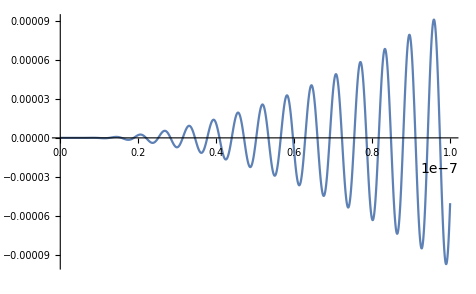

```mathematica
g1=Plot[ex[t], {t, 0, T}, PlotRange->All]
```

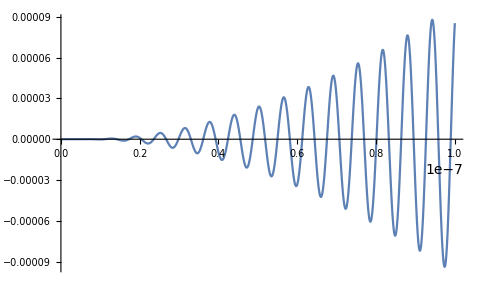

```mathematica
g2=Plot[ey[t], {t, 0,T}, PlotRange->All]
```

```mathematica
f1 [t_,k_]:= (1- 2/(ⅇ^(ϕ*(t-k*T))+ⅇ^(-ϕ*(t-k*T))));
f2[t_]:=(Sin[ψ*t])^2
f3[t_]:=Sin[w*t];
f4[t_,k_]:=(1- 2/(ⅇ^(ϕ*(t-(k+1)*T))+ⅇ^(-ϕ*(t-(k+1)*T))));
f5[t_]:=(1 - 1/(1+β*(Sin[ψ*t])^2));
bunch[k_]:=Plot[(f1[t,k]*f2[t]*f3[t]*f4[t,k]*f5[t])^2, {t,T*k, (k+1)*T}, PlotRange->All];
```

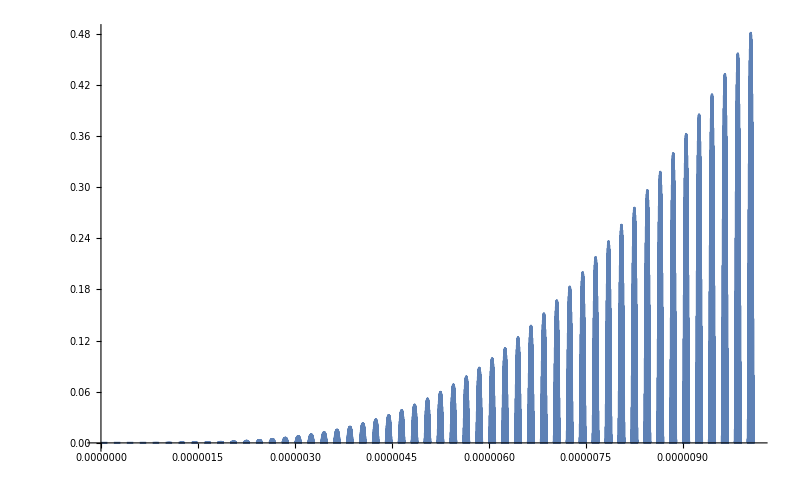

```mathematica
Show[Table[bunch[i],{i,0,100,2}]]
```